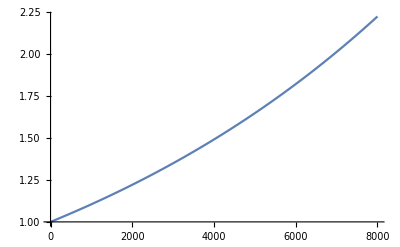

```mathematica
Plot[Exp[d/10000],{d,0,8000}]
```

```mathematica
Select[Range[0,10000],Exp[#/10000]≤(4+Pi)/4&]//Max
Select[Range[0,10000],Exp[#/10000]≥(3+Pi)/4&]//Min
```

5796

4288

```mathematica
f[a_,b_,c_,d_]:=Exp[a/10000]+Exp[b/10000]+Exp[c/10000]+Exp[d/10000]
```

```mathematica
f[5796,5796,5796,5796]-4-Pi//N
f[4288,4288,4288,4288]-4-Pi//N
```

-0.000296021

-0.999937